```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210519_time_windows_and_OR_model/deleting_reactions"];
```

```mathematica
Get["../../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
subsetpositionsforsequences=Import["../cases/subsetpositionsforsequences.mx"];
boundariesposdouble=Import["../cases/boundariesposdouble.mx"];
objfunctions=Import["C:/Users/serha/NonDrive/OR_model-objective_functions/+2+4objfunc_fxdbounds_-5and5_105pcs.mx"];
```

```mathematica
boundariesa=ReplacePart[ConstantArray[{-500,500},fluxexchanges],MapThread[#1->#2&,{boundariesposdouble,ConstantArray[{-50,50},Length@boundariesposdouble]}]];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,subsetpositions_,objectivefunctions_]:=Module[{solutionvectors},
solutionvectors=Chop[Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}],10^-5]]
```

```mathematica
AbsoluteTiming[solutionvectorsminus1toplus1=Quiet@Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundariesa,fluxexchanges,i[[1]],i[[2]]],{i,MapThread[{#1,#2}&,{subsetpositionsforsequences,objfunctions}]}];]
```

{5235.91,Null}

```mathematica
Dimensions@solutionvectorsminus1toplus1
```

{200,300,1008}

```mathematica
(*Export["C:/Users/serha/NonDrive/OR_model-solution_vectors/+2+4solutionvectors_fxdcoeffs_-50and50_210pcs.mx",solutionvectorsminus1toplus1]*)
```

C:/Users/serha/NonDrive/OR_model-solution_vectors/+2+4solutionvectors_fxdcoeffs_-50and50_210pcs.mx

```mathematica
solutionvectors=Import["C:/Users/serha/NonDrive/OR_model-solution_vectors/+2+4solutionvectors_fxdcoeffs_-50and50_210pcs.mx"];
```

```mathematica
SeedRandom@25;
deletionlist=Table[RandomInteger[1008,i],{i,Range[10,100,10]}];
```

```mathematica
solutionvectorsreactionsdeleted=Table[Partition[Delete[Transpose@Flatten[solutionvectors,1],Partition[deletionlist[[i]],1]]//Transpose,300],{i,10}];
```

```mathematica
objfunctionsreactionsdeleted=Table[Partition[Delete[Transpose@Flatten[objfunctions,1],Partition[deletionlist[[i]],1]]//Transpose,300],{i,10}];
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
AbsoluteTiming[featuredatalist=Table[Table[MapThread[Dot,{objfunctionsreactionsdeleted[[j]][[i]],solutionvectorsreactionsdeleted[[j]][[i]]}],{i,200}],{j,10}];]
```

{122.509,Null}

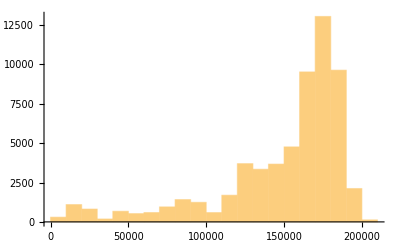
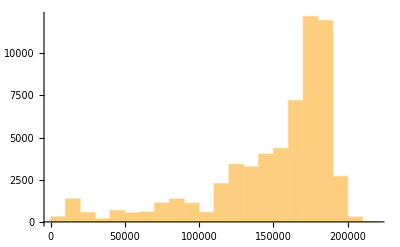
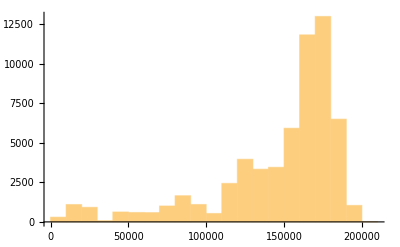
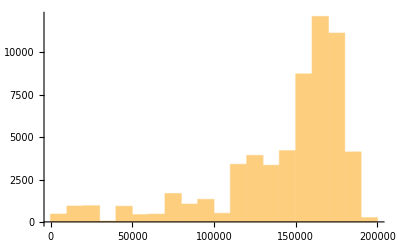
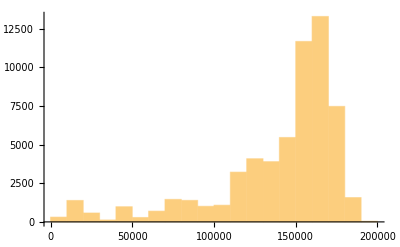
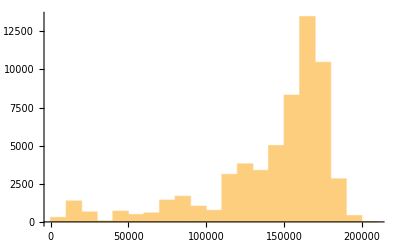
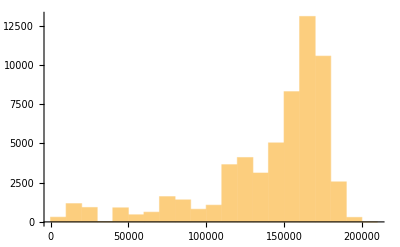
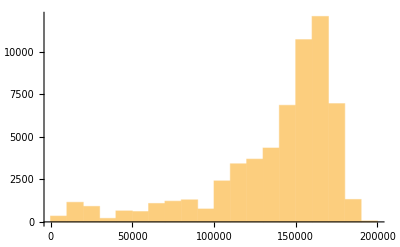

```mathematica
datafulllist=Table[Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Partition[Flatten[featuredatalist[[j]],1],1],2],{j,10}];
Table[Histogram@datafulllist[[i]][[All,3]],{i,10}]
```

```mathematica
AbsoluteTiming[widthdataFixedstep2=Table[snetworkdatabinned[3,5000,datafulllist[[i]]],{i,10}];]
```

{44.6068,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataFixedstep2[[i]][[1]],widthdataFixedstep2[[i]][[2]],2,7,400,Green],{i,10}];
graphsandnodenumbers12[[All,2]]
```

{41,43,40,40,40,39,40,39,38,40}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{127.638,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{41,43,40,40,40,39,40,39,38,40}

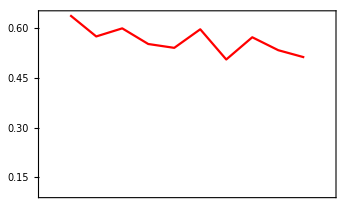
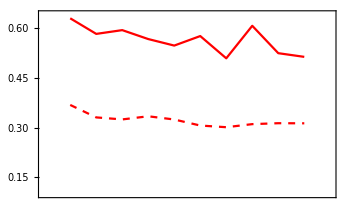
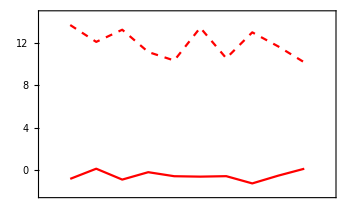

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataFixedbucket2=Table[snetworkdatafxdbucket[3,bucketnode12[[i]],datafulllist[[i]]],{i,10}];]
```

{14.7471,Null}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataFixedbucket2[[i]][[1]],widthdataFixedbucket2[[i]][[2]],1.5,7,400,Green],{i,10}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{88.0962,Null}

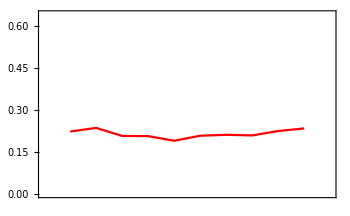
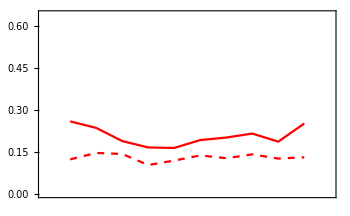
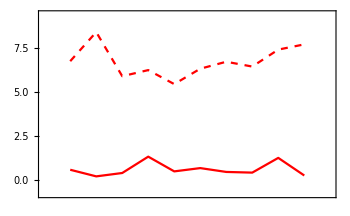

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/fxd_coeffs/-50+50_210_(2,4)-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/fxd_coeffs/-50+50_210_(2,4)-modularityvalues-fss.mx

plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-erd-modularityvalues-fss.mx

plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-comm-modularityvalues-fss.mx

plot_values/fxd_coeffs/-50+50_210_(2,4)-zscores-fss.mx

plot_values/fxd_coeffs/-50+50_210_(2,4)-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-erd-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-comm-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-50+50_210_(2,4)-zscores-fbs.mx